For a classical harmonic oscillator with initial conditions (x(0), v(0)) = (0,p/m),

```mathematica
x[t_] := p/(m ω)Sin[ω t];
x'[t]
```

(p Cos[t ω])/m

```mathematica
ℒ[t_]:= 1/2 m x'[t]^2-1/2 m ω^2 x[t]^2
```

```mathematica
TrigReduce[ℒ[t]]
```

(p^2 Cos[2 t ω])/(2 m)

Which accumulates a phase of the form

```mathematica
Integrate[ℒ[t],{t,0,T}]//FullSimplify
```

(p^2 Sin[2 T ω])/(4 m ω)

If allowed to oscillate until returning to the origin (an integer number of half-periods) then the accumulated phase is zero:

```mathematica
Integrate[ℒ[t],{t,0,π/ω}]
```

0

If we instead introduced a mirror at some variable θ we would get

```mathematica
MirroredPhase = 1/ℏ(Integrate[ℒ[t],{t,0,θ}]+Integrate[ℒ[t],{t,π/ω-θ,π/ω}])/.p-> m v
```

(m v^2 Sin[2 θ ω])/(2 ω ℏ)

A second beamsplitter pulse would then recombine the paths and produce output from two ports with a phase that is periodic in the delay interval θ,

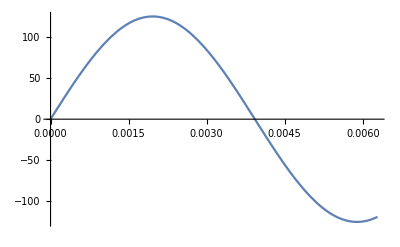

```mathematica
Plot[MirroredPhase/.{v->.1,m->6.64*10^-27,ω->400,ℏ->6.63*10^-34},{θ,0,2π*10^-3}]
```

Which would produce a phase-modulated interference pattern:

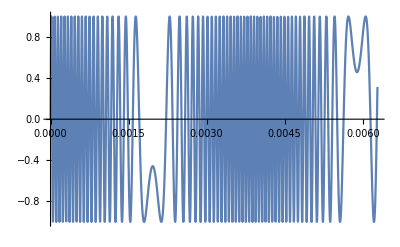

```mathematica
Plot[Sin[MirroredPhase]/.{v->.1,m->6.64*10^-27,ω->400,ℏ->6.63*10^-34},{θ,0,2π*10^-3}]
```